### Code (new method of calling new header)

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### Tests

Select a ruleset to investigate, possibly by giving its reduced rank index, giving it some convenient name:

```mathematica
rs=FromReducedRankIndex[]
```

FromReducedRankIndex[]

We can pull out the ruleset itself:

```mathematica
rs[["RuleSet"]]
```

Part::pspec1: Part specification RuleSet is not applicable.

FromReducedRankIndex[]⟦RuleSet⟧

We generate the sessie and its causal network, again giving it a convenient name:

```mathematica
sss=SSS[rs[["RuleSet"]], "A",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,338.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

Part::pspec1: Part specification RuleSet is not applicable.

Then we look at its Net, and create the list of lists of integers that we will summarize:

```mathematica
sss[["Net"]]//Short
```

Part::pspec1: Part specification Net is not applicable.

SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,«10»,SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧

```mathematica
nds=ToNetDifferenceSets[sss[["Net"]]]
```

Part::pspec1: Part specification Net is not applicable.

ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],DirectedEdges→True,ImageSize→304.,NetSize→{Automatic,338.},SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧]

You will probably need to limit the part of the nds list that you try to compact, omitting the incomplete sets at the end of the list. In theory it’s not needed to start later than the beginning of the list.

```mathematica
Position[nds,25]
```

{}

```mathematica
nds[[1;;349]]
```

Part::take: Cannot take positions 1 through 349 in ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],«6»]⟦Net⟧].

ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],DirectedEdges→True,ImageSize→304.,NetSize→{Automatic,338.},SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧]⟦1;;349⟧

Try the reduction:

```mathematica
rsl=ReduceSetList[nds[[1;;349]]]
```

Part::take: Cannot take positions 1 through 349 in ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],«6»]⟦Net⟧].

ReduceSetList[ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],DirectedEdges→True,ImageSize→304.,NetSize→{Automatic,338.},SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧]⟦1;;349⟧]

The most compressed part is

```mathematica
{ExpandAll[%]}
```

Part::take: Cannot take positions 1 through 349 in ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],«6»]⟦Net⟧].

Part::pspec1: Part specification Net is not applicable.

Part::pspec1: Part specification RuleSet is not applicable.

General::stop: Further output of Part::pspec1 will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 349 in ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],«6»]⟦Net⟧].

{ReduceSetList[ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],DirectedEdges→True,ImageSize→304.,NetSize→{Automatic,338.},SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧]⟦1;;349⟧]}

```mathematica
GraphPlot[FromNetDifferenceSets@%]
```

GraphPlot::graph: A graph object is expected at position 1 in GraphPlot[FromNetDifferenceSets[{ReduceSetList[ToNetDifferenceSets[SSS[«16»]⟦Net⟧]⟦1;;349⟧]}]].

GraphPlot[FromNetDifferenceSets[{ReduceSetList[ToNetDifferenceSets[SSS[FromReducedRankIndex[]⟦RuleSet⟧,A,400,SSSMax→75,NetMax→100,NetSize→{600,Automatic},SSSSize→{Automatic,380},HighlightMethod→None,RulePlacement→Left,VertexLabels→Placed[Automatic,Tooltip],DirectedEdges→True,ImageSize→304.,NetSize→{Automatic,338.},SSSSize→{Automatic,486.},IconSize→{Automatic,31.8},VertexSize→Automatic]⟦Net⟧]⟦1;;349⟧]}]]

===
Experimenting with Sessies
6308190100: {“AB” -> “BA”, “AA” -> “B”, “B” -> “AAA”}
6355450520: {“ABB” -> “AAA”, “A” -> “B”, “B” -> “AA”}
642296934875: {“A” -> “BC”, “CB” -> “A”, “B” -> “AAAA”}
702927424475: {“AA” -> “”, “AB” -> “BA”, “A” -> “BB”, “B” -> “AAA”}

```mathematica
rs01 = FromReducedRankIndex[6308190100]
rs02 = FromReducedRankIndex[6355450520]
rs03 = FromReducedRankIndex[642296934875]
rs04 = FromReducedRankIndex[702927424475]
```

<|Index→6308190100,QCode→34243232424233,RuleSet→{AB→BA,AA→B,B→AAA}|>

<|Index→6355450520,QCode→34342332242423,RuleSet→{ABB→AAA,A→B,B→AA}|>

<|Index→642296934875,QCode→24344244342242333,RuleSet→{A→BC,CB→A,B→AAAA}|>

<|Index→702927424475,QCode→31342432243424233,RuleSet→{AA→,AB→BA,A→BB,B→AAA}|>




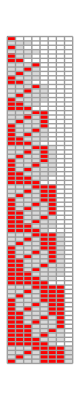
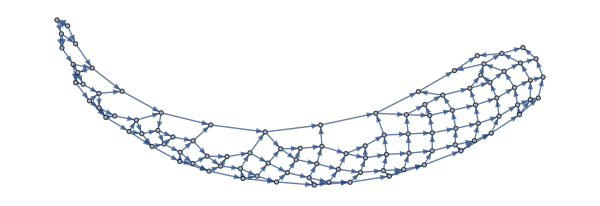
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules: | -Graphics--Graphics-

```mathematica
sss=SSS[rs01[["RuleSet"]], "B",400, (* choose an appropriate initial state string, and # steps *)
(* options *) SSSMax->75,NetMax->100,NetSize->{600,Automatic},SSSSize->{Automatic,380},HighlightMethod->None,RulePlacement->Left,VertexLabels->Placed[Automatic,Tooltip],DirectedEdges->True,ImageSize->304.,NetSize->{Automatic,500.},SSSSize->{Automatic,486.},IconSize->{Automatic,31.8},VertexSize->Automatic]; (* options can be changed or omitted, but these are reasonable choices *)
```

```mathematica
rs01[["RuleSet"]]
SSSInitialState[rs01[["RuleSet"]]]
```

{AB→BA,AA→B,B→AAA}

AABAB

```mathematica
netds = ToNetDifferenceSets[sss[["Net"]]];
reduced = ReduceSetList[netds];
(*TypeOf[reduced]*)
```